```mathematica
Generating a 3-mode Quantum Transducer from Langevin Equations
```

```mathematica
Shoumik Chowdhury  2/10/2020
```

```mathematica
Preliminaries
```

```mathematica
Id[n_]:=IdentityMatrix[n] 
mJn[n_]:=ArrayFlatten[Id[n]⊗({{0, 1}, {-1, 0}})] ; (* Symplectic matrix in QP basis *)
mJqqn[n_] :=ArrayFlatten[({{0, 1}, {-1, 0}})⊗Id[n]]; (*Symplectic matrix in QQ basis *)
sympQn[mS_, n_]:=1-Norm[mSᵀ.mJn[n].mS-mJn[n]]; (* Test for symplecticity *)

n = 6; (* For a 3-mode transducer we work with n = 6 *)
mJ = mJn[n];
sympQ[mS_] := sympQn[mS, n]
```

#### Helper Functions

```mathematica
({{Note that "⟦{1,7,2,8,3,9,4,10,5,11,6,12}, {1,7,2,8,3,9,4,10,5,11,6,12}⟧" converts from "qqpp" -> "qpqp"}, {Meanwhile "⟦{1,3,5,7,9,11,2,4,6,8,10,12}, {1,3,5,7,9,11,2,4,6,8,10,12}⟧" converts "qpqp" -> "qqpp".}})
```

```mathematica
QQtoQP[n0_, M0_] :=
(* Converts a matrix from QQ basis to QP basis*) 
Module[{n=n0, M=M0},
	ord= Flatten[Table[{i, n+i}, {i, 1, n}]];
	Return[M⟦ord, ord⟧]
]

QPtoQQ[n0_, M0_] := 
(* Converts a matrix from QP basis to QQ basis*)
Module[{n=n0, M=M0},
	odds = Table[{i}, {i, 1, 2n, 2}];
	evens = Table[{i+1}, {i, 1, 2n, 2}];
	ord = Flatten[Join[odds,evens]];
	Return[M⟦ord, ord⟧]
] 

(*Generate random n×n symplectic matrix in QQ basis and convert to QP*)
rSymMat[{a_,b_},c_]:=(UpperTriangularize[#]+UpperTriangularize[#,1]ᵀ)&@RandomReal[{a,b},{c,c}];
rSympMat[a_,b_, n_]:=QQtoQP[n, Id[2n]-Inverse[(mJqqn[n].rSymMat[{a,b},2n]+1/2 Id[2n])]]; 
(*Generate random local operations for n = 6*)
randomLocal[a_, b_] := ArrayFlatten[({{rSympMat[a,b, 1], 0, 0, 0, 0, 0}, {0, rSympMat[a,b, 1], 0, 0, 0, 0}, {0, 0, rSympMat[a,b, 1], 0, 0, 0}, {0, 0, 0, rSympMat[a,b, 1], 0, 0}, {0, 0, 0, 0, rSympMat[a,b, 1], 0}, {0, 0, 0, 0, 0, rSympMat[a,b, 1]}})];
```

```mathematica
Theory
```

References:"Cavity Optomechanics" (https: //arxiv.org/abs/1303.0733) and KL paper (https: //www.nature.com/articles/nphys2911)
Hamiltonian given by   (a⃗)^†.H.a⃗, where  a⃗ = {a_o, a_m, a_μ, a_o^†, a_m^†, a_μ^†} and  (a⃗)^†= {(a_o)^†,(a_m)^†,(a_μ)^†,a_o,a_m,a_μ}
H = 1/2(Δ_o | g_om | 0 | 0 | g_om | 0
g_om | ω_m | g_μm | g_om | 0 | g_μm
0 | g_μm | Δ_μ | 0 | g_μm | 0
0 | g_om | 0 | Δ_o | g_om | 0
g_om | 0 | g_μm | g_om | ω_m | g_μm
0 | g_μm | 0 | 0 | g_μm | Δ_μ) := (A | B
B^† | P)
Linearized Hamiltonian:H=Δ_o ((a_o)^† a_o+1/2)+Δ_μ ((a_μ)^† a_μ+1/2)+ω_m ((a_m)^† a_m+1/2)+g_om (a_o+(a_o)^†) (a_m+(a_m)^†)+g_μm (a_μ+(a_μ)^†) (a_m+(a_m)^†)   
Langevin Eq: d/dt (a
a^†)= I [(a | a^†)H(a
a^†), (a
a^†)] - 1/2(κ | 0
0 | κ)(a
a^†)+(√κ | 0
0 | √κ)(A_in
A_in^†) (*1mode example *)
Fourier Transform: â[ω] ∝∫â(t) e^(-I ω t)dt       and     (â[-ω])^† ∝∫â (t)^† e^(-I ω t)dt
Langevin → (I ω | □
□ | Iω)(a[ω]
a[-ω]^†)= I(-A^⋆-P | -B^†
B^ᵀ | A+P^⋆)(a[ω]
a[-ω]^†)- 1/2(κ | 0
0 | κ)(a[ω]
a[-ω]^†) + (√κ | 0
0 | √κ)(A_in[ω]
A_in[-ω]^†)
Thus →    T(a[ω]
a[-ω]^†) = Y(A_in[ω]
A_in[-ω]^†); then extend this to a[-ω] and a[ω]^†modes to get full matrix
Input Output relation: A_out[ω] = A_in[ω] - √κ a[ω]; gives matrix equations (A⃗)_out[ω] = (A⃗)_in[ω] - W(M^-1 W  (A⃗)_in)= S_complex(A⃗)_in

```mathematica
Setup and Initialization
```

```mathematica
T[ω_] := I({{ω, 0, 0, 0, 0, 0}, {0, ω, 0, 0, 0, 0}, {0, 0, ω, 0, 0, 0}, {0, 0, 0, ω, 0, 0}, {0, 0, 0, 0, ω, 0}, {0, 0, 0, 0, 0, ω}}) - I({{- Subscript[Δ, o]+I Subscript[κ, o]/2, -Subscript[g, om], 0, 0, -Subscript[g, om]/2, 0}, {-Subscript[g, om], - ωm+I Subscript[κ, m]/2, -Subscript[g, μm], -Subscript[g, om]/2, 0, -Subscript[g, μm]/2}, {0, -Subscript[g, μm], - Subscript[Δ, μ]+I Subscript[κ, μ]/2, 0, -Subscript[g, μm]/2, 0}, {0, Subscript[g, om]/2, 0, Subscript[Δ, o]+ I Subscript[κ, o]/2, Subscript[g, om], 0}, {Subscript[g, om]/2, 0, Subscript[g, μm]/2, Subscript[g, om], ωm+I Subscript[κ, m]/2, Subscript[g, μm]}, {0, Subscript[g, μm]/2, 0, 0, Subscript[g, μm], Subscript[Δ, μ]+ I Subscript[κ, μ]/2}})
```

```mathematica
M[ω_] := ({{T[ω], 0}, {0, T[-ω]}}) // ArrayFlatten
```

```mathematica
Y = ({{√Subscript[κ, o], 0, 0, 0, 0, 0}, {0, √Subscript[κ, m], 0, 0, 0, 0}, {0, 0, √Subscript[κ, μ], 0, 0, 0}, {0, 0, 0, √Subscript[κ, o], 0, 0}, {0, 0, 0, 0, √Subscript[κ, m], 0}, {0, 0, 0, 0, 0, √Subscript[κ, μ]}});
W = ({{Y, 0}, {0, Y}}) // ArrayFlatten;
```

```mathematica
Setting values
```

```mathematica
{Subscript[Δ, o], ωm, Subscript[Δ, μ], Subscript[κ, o], Subscript[κ, μ]} = {730, 560, 650, 1650, 1590}*1000 (*kHz -> Hz*)
{Subscript[κ, m], Subscript[g, om],Subscript[g, μm]} = {4,- 34000,0}  (*Hz*)
```

{730000,560000,650000,1650000,1590000}

{4,-34000,-23000}

```mathematica
Finding Scattering Matrices
```

```mathematica
(SComplex= Id[12] - W.Inverse[M[ω]].W );
```

We want to change from basis A to basis B
(A) ao[+ω], am[+ω],aμ[+ω],(ao[-ω])^†,(am[-ω])^†,(aμ[-ω])^†,ao[-ω],am[-ω],aμ[-ω], ...
(B) qo[+ω], po[+ω],qm[+ω], pm[+ω], qμ[+ω], pμ[+ω],qo[-ω], po[-ω], ...

```mathematica
U = 1/(√2)({{1, I, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, I, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, I, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, -I, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, -I, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -I}, {0, 0, 0, 0, 0, 0, 1, I, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, I, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, I}, {1, -I, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, -I, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, -I, 0, 0, 0, 0, 0, 0}});
```

```mathematica
(S = Inverse[U].SComplex.U);
```

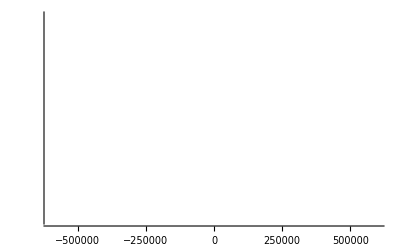

```mathematica
Plot[N[sympQ[S/.{ω->x}]] , {x, -600000, 600000}](* evaluate this numerically? *)
```

#### Symplectic Decoupling Algorithm

#### Part 1: Code to Decouple the first quadrature

```mathematica
Decouple1Q[mS0_, n0_, c0_, r0_] := 
(*This is a wrapper function to compute the local operations given input mS. We rotate column c -> row r *) 
Module[{mS = mS0, n=n0, c=c0, r =r0},
(* Tabular representations of column vector cv and row vectow rv in qpqp basis *)
cv=Table[{mS⟦i,c⟧,mS⟦i+1,c⟧},{i,1,2n, 2}];
rv=Table[{mS⟦r,i⟧,mS⟦r,i+1⟧},{i,1,2n, 2}];
(*we are going to rotate column c -> row r*)

ncv=Norm/@cv  /. 0 -> 1; (*list of norms of cv*)
nrv=Norm/@rv /. 0 -> 1;(*list of norms of rv*)
mL=Table[(({{rv⟦i,1⟧, -rv⟦i,2⟧}, {rv⟦i,2⟧, rv⟦i,1⟧}})/nrv⟦i⟧).({{nrv⟦i⟧/ncv⟦i⟧, 0}, {0, ncv⟦i⟧/nrv⟦i⟧}}).(({{cv⟦i,1⟧, cv⟦i,2⟧}, {-cv⟦i,2⟧, cv⟦i,1⟧}})/ncv⟦i⟧),{i,1,n}] /. ({{0, 0}, {0, 0}}) -> ({{1, 0}, {0, 1}}); 
(*List of local symplectic operations for all modes*)

mSL1qq=ArrayFlatten[({{DiagonalMatrix[mL⟦;;,1,1⟧], DiagonalMatrix[mL⟦;;,1,2⟧]}, {DiagonalMatrix[mL⟦;;,2,1⟧], DiagonalMatrix[mL⟦;;,2,2⟧]}})]; (*this gives a result in qqpp*)

mSL1 = QQtoQP[n, mSL1qq];
Return[mSL1]
]
```

```mathematica
Part 2: Code to Decouple the second quadrature
```

```mathematica
(* INSERT THE CODE HERE *)
```

```mathematica
Part 3: Running the algorithm!
```

```mathematica
mS = S  /. {ω -> 100000};
mSL1 = Decouple1Q[mS, n, 9, 9];
mS1 = mS.mJ.mSL1.mS;
{sympQ[mSL1], sympQ[mS1]}
Eigenvalues[mSL1.Transpose[mSL1]]
(N[mS1]) // MatrixForm
```

{1,1}

{1,1,1,1,1,1,1,1,1,1,1,1}

(1. | -0.00526313 | 0.000134467 | -0.000180017 | -0.000129086 | -0.00409061 | -0.00576757 | 0.000774744 | 0. | 0. | -0.00408214 | 0.000744859
0.00526313 | 1. | 0.000180017 | 0.000134467 | 0.00409061 | -0.000129086 | 0.000774744 | 0.00576757 | 0. | 0. | 0.000744859 | 0.00408214
0.000134467 | -0.000180017 | 0.280652 | 0.95981 | 0.0000914486 | -0.000131005 | -0.00009095 | 0.000088728 | 0. | 0. | -0.0000618114 | 0.0000662422
0.000180017 | 0.000134467 | -0.95981 | 0.280652 | 0.000131005 | 0.0000914486 | 0.000088728 | 0.00009095 | 0. | 0. | 0.0000662422 | 0.0000618114
-0.000129086 | -0.00409061 | 0.0000914486 | -0.000131005 | 0.997781 | -0.0666464 | -0.00411654 | 0.00041881 | 0. | 0. | -0.00291808 | 0.00043608
0.00409061 | -0.000129086 | 0.000131005 | 0.0000914486 | 0.0666464 | 0.997781 | 0.00041881 | 0.00411654 | 0. | 0. | 0.00043608 | 0.00291808
0.00576757 | 0.000774744 | 0.00009095 | 0.000088728 | 0.00411654 | 0.00041881 | -0.963609 | 0.267332 | 0. | 0. | 0.00198914 | 0.00615595
0.000774744 | -0.00576757 | 0.000088728 | -0.00009095 | 0.00041881 | -0.00411654 | -0.267332 | -0.963609 | 0. | 0. | -0.00615595 | 0.00198914
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 0. | 0. | 0.
0.00408214 | 0.000744859 | 0.0000618114 | 0.0000662422 | 0.00291808 | 0.00043608 | 0.00198914 | 0.00615595 | 0. | 0. | -0.935865 | 0.352337
0.000744859 | -0.00408214 | 0.0000662422 | -0.0000618114 | 0.00043608 | -0.00291808 | -0.00615595 | 0.00198914 | 0. | 0. | -0.352337 | -0.935865)

```mathematica
mSL2 = Decouple1Q[mS1, n, 7, 7];
mS2 = mS1.mJ.mSL2.mS1;
{sympQ[mSL2], sympQ[mS2]}
Eigenvalues[mSL2.Transpose[mSL2]]
(N[mS2]) // MatrixForm
```

{1,1}

{1,1,1,1,1,1,1,1,1,1,1,1}

(-0.274032 | -0.961721 | -0.000418434 | -0.000163868 | -0.00781015 | 0.00244932 | 0. | 0. | 0. | 0. | 0.000780374 | -0.0082622
0.961721 | -0.274032 | 0.000163868 | -0.000418434 | -0.00244932 | -0.00781015 | 0. | 0. | 0. | 0. | -0.0082622 | -0.000780374
-0.000418434 | -0.000163868 | 0.855534 | -0.517746 | -0.000301113 | -0.000106896 | 0. | 0. | 0. | 0. | -0.0000939894 | -0.000154919
0.000163868 | -0.000418434 | 0.517746 | 0.855534 | 0.000106896 | -0.000301113 | 0. | 0. | 0. | 0. | -0.000154919 | 0.0000939894
-0.00781015 | 0.00244932 | -0.000301113 | -0.000106896 | -0.329868 | -0.94401 | 0. | 0. | 0. | 0. | 0.000743365 | -0.00585387
-0.00244932 | -0.00781015 | 0.000106896 | -0.000301113 | 0.94401 | -0.329868 | 0. | 0. | 0. | 0. | -0.00585387 | -0.000743365
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0.
-0.000780374 | -0.0082622 | 0.0000939894 | -0.000154919 | -0.000743365 | -0.00585387 | 0. | 0. | 0. | 0. | -0.0949309 | -0.995536
-0.0082622 | 0.000780374 | -0.000154919 | -0.0000939894 | -0.00585387 | 0.000743365 | 0. | 0. | 0. | 0. | 0.995536 | -0.0949309)

```mathematica
mSL3 = Decouple1Q[mS2, n, 11, 11];
mS3 = Chop[N[mS2.mJ.mSL3.mS2], 10^-10]; (* need "N" since we are hitting the bounds on Mathematica's numerical precision *) 
{sympQ[mSL3], sympQ[mS3]} 
Eigenvalues[mSL3.Transpose[mSL3]]
(Chop[N[mS3], 10^-10]) // MatrixForm
```

{1,1.}

{1,1,1,1,1,1,1,1,1,1,1,1}

(-0.358603 | -0.933346 | -0.000860578 | -0.000258701 | -0.0151196 | 0.00627316 | 0 | 0 | 0 | 0 | 0 | 0
0.933346 | -0.358603 | 0.000258701 | -0.000860578 | -0.00627316 | -0.0151196 | 0 | 0 | 0 | 0 | 0 | 0
-0.000860578 | -0.000258701 | 0.820622 | -0.57147 | -0.000617498 | -0.000164189 | 0 | 0 | 0 | 0 | 0 | 0
0.000258701 | -0.000860578 | 0.57147 | 0.820622 | 0.000164189 | -0.000617498 | 0 | 0 | 0 | 0 | 0 | 0
-0.0151196 | 0.00627316 | -0.000617498 | -0.000164189 | -0.407447 | -0.913082 | 0 | 0 | 0 | 0 | 0 | 0
-0.00627316 | -0.0151196 | 0.000164189 | -0.000617498 | 0.913082 | -0.407447 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0)

```mathematica
mSL4 = Decouple1Q[mS3, n, 3, 3];
mS4 = mS3.mJ.mSL4.mS3;

{sympQ[mSL4], sympQ[mS4]}
Eigenvalues[mSL4.Transpose[mSL4]]
(Chop[N[mS4], 10^-10]) // MatrixForm
```

{1.,1.}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

(-0.96762 | -0.250281 | 0 | 0 | -0.00753767 | 0.031854 | 0 | 0 | 0 | 0 | 0 | 0
0.250281 | -0.96762 | 0 | 0 | -0.031854 | -0.00753767 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.00753767 | 0.031854 | 0 | 0 | -0.977171 | -0.209917 | 0 | 0 | 0 | 0 | 0 | 0
-0.031854 | -0.00753767 | 0 | 0 | 0.209917 | -0.977171 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0)

```mathematica
R = ({{mS4⟦1, 5⟧, mS4⟦1, 6⟧}, {mS4⟦2, 5⟧, mS4⟦2, 6⟧}}) ;
T =  ({{mS4⟦5, 5⟧, mS4⟦5, 6⟧}, {mS4⟦6, 5⟧, mS4⟦6, 6⟧}});
{MatrixRank[R],MatrixRank[T], Det[R]}
```

{2,2,0.0010715}

```mathematica
(* This effective two mode transducer has classification [2,2] and χ = Det[R] = 0.09. Since 0 < χ < 1, this corresponds to a beamsplitter interaction*)
```

```mathematica
(Chop[N[mS], 10^-10]) // MatrixForm
(Chop[N[mS1], 10^-10]) // MatrixForm
(Chop[N[mS2], 10^-10]) // MatrixForm
(Chop[N[mS3], 10^-10]) // MatrixForm
(Chop[N[mS4], 10^-10]) // MatrixForm
```

(0.00316434 | -0.999999 | -0.000080042 | -0.0000803777 | -0.00204564 | 0.0000532921 | -0.000398838 | -0.00288224 | 0.0000573639 | -0.0000580328 | -0.000380544 | -0.00203959
0.999999 | 0.00316434 | 0.0000803777 | -0.000080042 | -0.0000532921 | -0.00204564 | -0.00288224 | 0.000398838 | -0.0000580328 | -0.0000573639 | -0.00203959 | 0.000380544
-0.000080042 | -0.0000803777 | 1. | -6.07239×10^-6 | -0.00005872 | -0.0000552933 | -0.0000509688 | -0.0000389583 | -1.91402×10^-9 | -1.33663×10^-8 | -0.0000376074 | -0.000026043
0.0000803777 | -0.000080042 | 6.07239×10^-6 | 1. | 0.0000552933 | -0.00005872 | -0.0000389583 | 0.0000509688 | -1.33663×10^-8 | 1.91402×10^-9 | -0.000026043 | 0.0000376074
-0.00204564 | 0.0000532921 | -0.00005872 | -0.0000552933 | -0.0596556 | -0.99822 | -0.000217588 | -0.00205744 | 0.0000420928 | -0.0000399315 | -0.000223841 | -0.00145817
-0.0000532921 | -0.00204564 | 0.0000552933 | -0.00005872 | 0.99822 | -0.0596556 | -0.00205744 | 0.000217588 | -0.0000399315 | -0.0000420928 | -0.00145817 | 0.000223841
0.000398838 | -0.00288224 | 0.0000509688 | -0.0000389583 | 0.000217588 | -0.00205744 | -0.267686 | -0.963507 | -0.000146164 | -0.00011105 | -0.0030751 | 0.00100347
-0.00288224 | -0.000398838 | -0.0000389583 | -0.0000509688 | -0.00205744 | -0.000217588 | 0.963507 | -0.267686 | 0.00011105 | -0.000146164 | -0.00100347 | -0.0030751
-0.0000573639 | -0.0000580328 | 1.91402×10^-9 | -1.33663×10^-8 | -0.0000420928 | -0.0000399315 | -0.000146164 | -0.00011105 | 1. | -8.71924×10^-6 | -0.000107825 | -0.0000742057
-0.0000580328 | 0.0000573639 | -1.33663×10^-8 | -1.91402×10^-9 | -0.0000399315 | 0.0000420928 | 0.00011105 | -0.000146164 | 8.71924×10^-6 | 1. | 0.0000742057 | -0.000107825
0.000380544 | -0.00203959 | 0.0000376074 | -0.000026043 | 0.000223841 | -0.00145817 | -0.0030751 | 0.00100347 | -0.000107825 | -0.0000742057 | -0.354769 | -0.934952
-0.00203959 | -0.000380544 | -0.000026043 | -0.0000376074 | -0.00145817 | -0.000223841 | -0.00100347 | -0.0030751 | 0.0000742057 | -0.000107825 | 0.934952 | -0.354769)

(1. | -0.00526313 | 0.000134467 | -0.000180017 | -0.000129086 | -0.00409061 | -0.00576757 | 0.000774744 | 0 | 0 | -0.00408214 | 0.000744859
0.00526313 | 1. | 0.000180017 | 0.000134467 | 0.00409061 | -0.000129086 | 0.000774744 | 0.00576757 | 0 | 0 | 0.000744859 | 0.00408214
0.000134467 | -0.000180017 | 0.280652 | 0.95981 | 0.0000914486 | -0.000131005 | -0.00009095 | 0.000088728 | 0 | 0 | -0.0000618114 | 0.0000662422
0.000180017 | 0.000134467 | -0.95981 | 0.280652 | 0.000131005 | 0.0000914486 | 0.000088728 | 0.00009095 | 0 | 0 | 0.0000662422 | 0.0000618114
-0.000129086 | -0.00409061 | 0.0000914486 | -0.000131005 | 0.997781 | -0.0666464 | -0.00411654 | 0.00041881 | 0 | 0 | -0.00291808 | 0.00043608
0.00409061 | -0.000129086 | 0.000131005 | 0.0000914486 | 0.0666464 | 0.997781 | 0.00041881 | 0.00411654 | 0 | 0 | 0.00043608 | 0.00291808
0.00576757 | 0.000774744 | 0.00009095 | 0.000088728 | 0.00411654 | 0.00041881 | -0.963609 | 0.267332 | 0 | 0 | 0.00198914 | 0.00615595
0.000774744 | -0.00576757 | 0.000088728 | -0.00009095 | 0.00041881 | -0.00411654 | -0.267332 | -0.963609 | 0 | 0 | -0.00615595 | 0.00198914
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0
0.00408214 | 0.000744859 | 0.0000618114 | 0.0000662422 | 0.00291808 | 0.00043608 | 0.00198914 | 0.00615595 | 0 | 0 | -0.935865 | 0.352337
0.000744859 | -0.00408214 | 0.0000662422 | -0.0000618114 | 0.00043608 | -0.00291808 | -0.00615595 | 0.00198914 | 0 | 0 | -0.352337 | -0.935865)

(-0.274032 | -0.961721 | -0.000418434 | -0.000163868 | -0.00781015 | 0.00244932 | 0 | 0 | 0 | 0 | 0.000780374 | -0.0082622
0.961721 | -0.274032 | 0.000163868 | -0.000418434 | -0.00244932 | -0.00781015 | 0 | 0 | 0 | 0 | -0.0082622 | -0.000780374
-0.000418434 | -0.000163868 | 0.855534 | -0.517746 | -0.000301113 | -0.000106896 | 0 | 0 | 0 | 0 | -0.0000939894 | -0.000154919
0.000163868 | -0.000418434 | 0.517746 | 0.855534 | 0.000106896 | -0.000301113 | 0 | 0 | 0 | 0 | -0.000154919 | 0.0000939894
-0.00781015 | 0.00244932 | -0.000301113 | -0.000106896 | -0.329868 | -0.94401 | 0 | 0 | 0 | 0 | 0.000743365 | -0.00585387
-0.00244932 | -0.00781015 | 0.000106896 | -0.000301113 | 0.94401 | -0.329868 | 0 | 0 | 0 | 0 | -0.00585387 | -0.000743365
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
-0.000780374 | -0.0082622 | 0.0000939894 | -0.000154919 | -0.000743365 | -0.00585387 | 0 | 0 | 0 | 0 | -0.0949309 | -0.995536
-0.0082622 | 0.000780374 | -0.000154919 | -0.0000939894 | -0.00585387 | 0.000743365 | 0 | 0 | 0 | 0 | 0.995536 | -0.0949309)

(-0.358603 | -0.933346 | -0.000860578 | -0.000258701 | -0.0151196 | 0.00627316 | 0 | 0 | 0 | 0 | 0 | 0
0.933346 | -0.358603 | 0.000258701 | -0.000860578 | -0.00627316 | -0.0151196 | 0 | 0 | 0 | 0 | 0 | 0
-0.000860578 | -0.000258701 | 0.820622 | -0.57147 | -0.000617498 | -0.000164189 | 0 | 0 | 0 | 0 | 0 | 0
0.000258701 | -0.000860578 | 0.57147 | 0.820622 | 0.000164189 | -0.000617498 | 0 | 0 | 0 | 0 | 0 | 0
-0.0151196 | 0.00627316 | -0.000617498 | -0.000164189 | -0.407447 | -0.913082 | 0 | 0 | 0 | 0 | 0 | 0
-0.00627316 | -0.0151196 | 0.000164189 | -0.000617498 | 0.913082 | -0.407447 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0)

(-0.96762 | -0.250281 | 0 | 0 | -0.00753767 | 0.031854 | 0 | 0 | 0 | 0 | 0 | 0
0.250281 | -0.96762 | 0 | 0 | -0.031854 | -0.00753767 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.00753767 | 0.031854 | 0 | 0 | -0.977171 | -0.209917 | 0 | 0 | 0 | 0 | 0 | 0
-0.031854 | -0.00753767 | 0 | 0 | 0.209917 | -0.977171 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0)